```mathematica
Get["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\Mathematica\\CDTFunctions.wl"]
```

```mathematica
data = Import["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data\\Statistical_Volume_256_TimeSize_16_stepsize_40_sample_100.csv"]
```

Syntax::bktmcp: Expression "Import[C:\Users\jacks\Documents\GitHub\cdt_rust\data\Statistical_Volume_1024_TimeSize_32_stepsize_20_sample_100.csv" has no closing "]".

```mathematica
sorted = SortBy[data,-#[[2]]&];
```

```mathematica
sorted[[234]]
```

{431_37_11_2_2_9_5_3_3_3_2_2_3_1_2_4_8_5_2_3_5_4_3_2_2_2_6_7_12_10_19_235,19579.9}

```mathematica
Mean[Table[N[Oscilatory[ToExpression@ StringSplit[sorted[[i,1]],"_"]]],{i,100}]]
```

8.36023

```mathematica
Mean[Table[N[Oscilatory[ToExpression@ StringSplit[sorted[[-i,1]],"_"]]],{i,100}]]
```

8.4767

```mathematica
Oscilatory[l_]:=Sqrt[Mean[Differences[l]^2]]
```

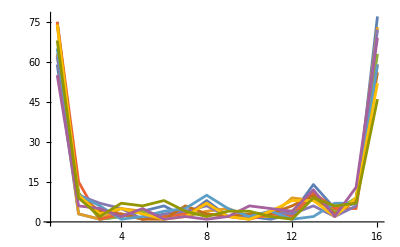

```mathematica
ListLinePlot[Table[N[ToExpression@ StringSplit[sorted[[i,1]],"_"]],{i,10}],PlotRange->All]
```

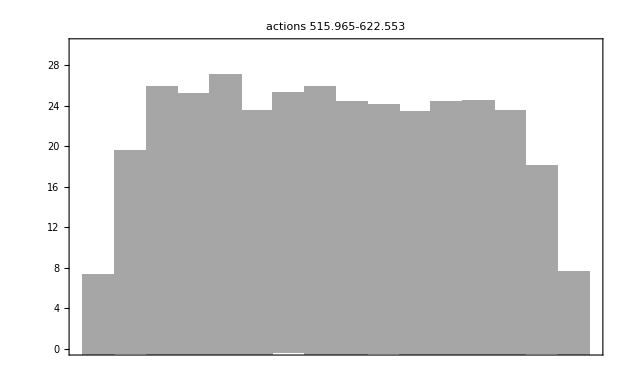

```mathematica
a = DistributionChart[Transpose[Table[N[ToExpression@ StringSplit[sorted[[-i,1]],"_"]],{i,1000}]],PlotRange->{0,30},ChartElementFunction->ChartElementData["Density"],ChartStyle-> {Directive[EdgeForm[None],Orange]},BarSpacing->0,PlotLabel-> "actions "<>ToString[sorted[[-1,2]]]<>"-"<>ToString[sorted[[-1000,2]]],PlotRange->All]
```

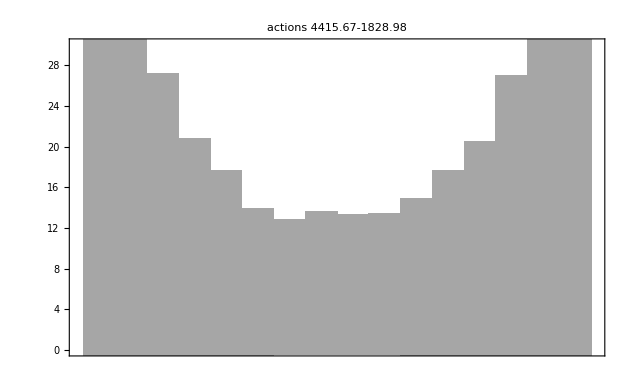

```mathematica
b = DistributionChart[Transpose[Table[N[ToExpression@ StringSplit[sorted[[i,1]],"_"]],{i,1000}]],PlotRange->{0,30},ChartElementFunction->ChartElementData["Density"], ChartStyle-> {Directive[EdgeForm[None],Blue]},BarSpacing->0,PlotLabel-> "actions "<>ToString[sorted[[1,2]]]<>"-"<>ToString[sorted[[1000,2]]],PlotRange->All]
```

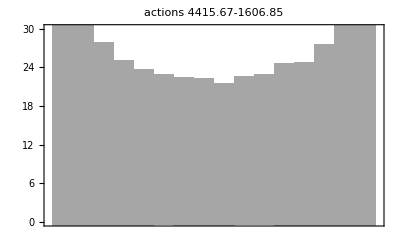

```mathematica
b = DistributionChart[Transpose[Table[N[ToExpression@ StringSplit[sorted[[RandomInteger[1000000],1]],"_"]],{i,10000}]],PlotRange->{0,30},ChartElementFunction->ChartElementData["Density"], ChartStyle-> {Directive[EdgeForm[None],Blue]},BarSpacing->0,PlotLabel-> "actions "<>ToString[sorted[[1,2]]]<>"-"<>ToString[sorted[[10000,2]]],PlotRange->All]
```